# Ejercicio 4.13

## Isaac Ayala A01184862

## Datos

```mathematica
dataMotor1800rpm={
{0,5},{0.125,33.5},{0.25,67},{0.5,134},{0.625,160},{0.75,175},{0.875,190},{1,200},{1.25,214},{1.5,223}
};
```

```mathematica
Pnom=20*10^3;
Vt=200;
nm=1800;

Ra=0.1;
Rfw=150;
RfcMin=0;
Rfmin=Rfw+RfcMin;

IfFullLoad=1.25;

Rsr=0.04;
Nf=1200;
```

```mathematica
VtRfmin=Table[{dataMotor1800rpm[[i,1]],Rfmin*dataMotor1800rpm[[i,1]]},{i,1,Length[dataMotor1800rpm]}];
```

## Fórmulas

```mathematica
ifMag=ifEle-ifAR+Nsr*IaNom/Nf;
```

Obtención de la ecuación para Ea

```mathematica
a[j_]:=dataMotor1800rpm[[j+1,2]];
x[j_]:=dataMotor1800rpm[[j+1,1]];
h[j_]:=x[j+1]-x[j];
```

```mathematica
matrix2=Table[
Which[
i==j,h[i-1],
i==j-1,2(h[i-1]+h[i]),
i==j-2,h[i],
i≠ j||i≠j-1||i≠j-2,0
],
{i,Length[dataMotor1800rpm]-2},
{j,Length[dataMotor1800rpm]}];
```

```mathematica
res=Table[
3/h[j](a[j+1]-a[j])-3/h[j-1](a[j]-a[j-1]),
{j,Length[dataMotor1800rpm]-2}
];
```

```mathematica
sol=LinearSolve[matrix2,res] ;
```

```mathematica
c[j_]:=LinearSolve[matrix2,res] [[j+1]];
```

```mathematica
d[j_]:=1/(3h[j])(c[j+1]-c[j]);
```

```mathematica
b[j_]:=1/h[j](a[j+1]-a[j])-h[j]/3(2c[j]+c[j+1]);
```

```mathematica
Table[
{a[i]+b[i]*(y-x[i])+c[i]*(y-x[i])^2+d[i]*(y-x[i])^3,
x[i]≤y≤x[i+1]},
{i,0,Length[dataMotor1800rpm]-2}]
```

{{5+213.946 y+57.6827 y^2+438. y^3,0≤y≤0.125},{33.5+248.898 (-0.125+y)+221.933 (-0.125+y)^2-552.924 (-0.125+y)^3,0.125≤y≤0.25},{67+278.463 (-0.25+y)+14.5863 (-0.25+y)^2-225.749 (-0.25+y)^3,0.25≤y≤0.5},{134+243.428 (-0.5+y)-154.725 (-0.5+y)^2-1029.59 (-0.5+y)^3,0.5≤y≤0.625},{160+156.485 (-0.625+y)-540.821 (-0.625+y)^2+1991.54 (-0.625+y)^3,0.625≤y≤0.75},{175+114.633 (-0.75+y)+206.008 (-0.75+y)^2-1304.58 (-0.75+y)^3,0.75≤y≤0.875},{190+104.983 (-0.875+y)-283.21 (-0.875+y)^2+666.781 (-0.875+y)^3,0.875≤y≤1},{200+65.4356 (-1+y)-33.1673 (-1+y)^2-18.3009 (-1+y)^3,1≤y≤1.25},{214+45.4206 (-1.25+y)-46.893 (-1.25+y)^2+36.843 (-1.25+y)^3,1.25≤y≤1.5}}

```mathematica
Ea[y_]:=Piecewise[{{5+213.94591425659797 y+57.68265044979452 y^2+438.0002839793742 y^3,0≤y≤0.125},{33.5+248.89784018057978 (-0.125+y)+221.93275694205985 (-0.125+y)^2-552.923827093585 (-0.125+y)^3,0.125≤y≤0.25},{67+278.462725021083 (-0.25+y)+14.586321781965466 (-0.25+y)^2-225.74888746518906 (-0.25+y)^3,0.25≤y≤0.5},{134+243.42796951234277 (-0.5+y)-154.72534381692634 (-0.5+y)^2-1029.5872982545266 (-0.5+y)^3,0.5≤y≤0.625},{160+156.48472895243026 (-0.625+y)-540.8205806623738 (-0.625+y)^2+1991.541992343453 (-0.625+y)^3,0.625≤y≤0.75},{175+114.6331146779362 (-0.75+y)+206.0076664664211 (-0.75+y)^2-1304.5806711192859 (-0.75+y)^3,0.75≤y≤0.875},{190+104.98281233582502 (-0.875+y)-283.21008520331117 (-0.875+y)^2+666.7806921336879 (-0.875+y)^3,0.875≤y≤1},{200+65.43563597876388 (-1+y)-33.16732565317819 (-1+y)^2-18.300873047509278 (-1+y)^3,1≤y≤1.25},{214+45.42055945576674 (-1.25+y)-46.89298043881015 (-1.25+y)^2+36.8429704629727 (-1.25+y)^3,1.25≤y≤1.5}}];
```

## Desarrollo

1.

(a)

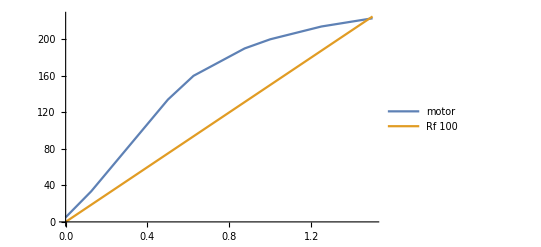

```mathematica
ListLinePlot[{dataMotor1800rpm,VtRfmin},PlotLegends->{"motor","Rf 100"}]
```

```mathematica
NSolve[Ea[y]-Rfmin*y==0,y]
```

{{y→1.48344}}

```mathematica
Emax=Ea[y]/.y->1.4834421812371472
```

222.516

(b)

```mathematica
iaNom=Pnom/Vt
```

100

```mathematica
Rfb=Vt/IfFullLoad
```

160.

```mathematica
Rfcb=Rfb-Rfw
```

10.

(c)

```mathematica
Eac=Vt+iaNom*Ra
```

210.

```mathematica
PFullLoad=Eac*iaNom
```

21000.

```mathematica
ωmFullLoad=nm*Pi/30
```

60 π

```mathematica
ΓFullLoad=PFullLoad/ωmFullLoad
```

111.408

(d)

```mathematica
VtRf160=Table[{dataMotor1800rpm[[i,1]],Rfb*dataMotor1800rpm[[i,1]]},{i,1,Length[dataMotor1800rpm]}];
```

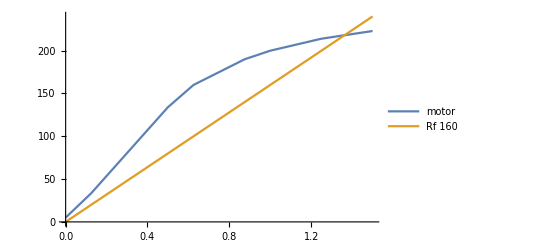

```mathematica
plot1=ListLinePlot[{dataMotor1800rpm,VtRf160},PlotLegends->{"motor","Rf 160"}]
```

```mathematica
ΔV=Eac-Vt
```

10.

```mathematica
NSolve[Ea[y]==Eac]
```

{{y→1.16856}}

```mathematica
IfAr=IfFullLoad-ia/.ia->1.168563446773787
```

0.0814366

(e)

```mathematica
Vte=Table[{dataMotor1800rpm[[i,1]],160*dataMotor1800rpm[[i,1]]+60},{i,1,Length[dataMotor1800rpm]}];
```

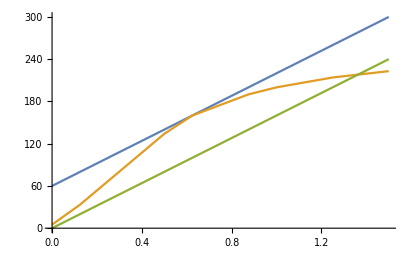

```mathematica
ListLinePlot[{Vte,dataMotor1800rpm,VtRf160}]
```

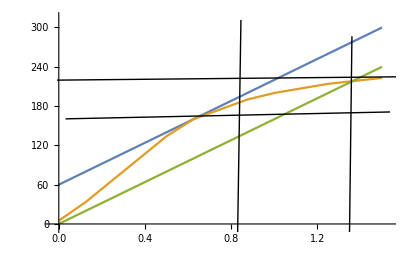

```mathematica
NSolve[Ea[y]==160y+60,y]
```

{{y→-0.375},{y→0.618418},{y→0.625}}

```mathematica
Ea[y]/.y->0.625
```

160.

```mathematica
NSolve[Ea[0.625]==160y,y]
```

{{y→1.}}

```mathematica
ΔV2=Max[Table[160-160i,{i,0.85,0.9,0.01}]]
```

24.

```mathematica
IaMax=ΔV2/Ra
```

240.

2.

(a)

```mathematica
img=-Graphics-
```

-Graphics-

```mathematica
Grid[{{"Donde"},{"Vt",Vt},{"Rsr",Rsr},{"Ra",Ra},{"Rfw",Rfw}}]
```

Donde | 
Vt | 200
Rsr | 0.04
Ra | 0.1
Rfw | 150

(b)

```mathematica
Ea2b=Vt+iaNom(Ra+Rsr)
```

214.

```mathematica
NSolve[Ea[y]==Ea2b,y](** Obtener If mag **)
```

{{y→1.25}}

```mathematica
IfMag=1.25;
```

```mathematica
NSolve[Ea[y]==Vt,y]
```

{{y→1.}}

```mathematica
IfElec=1;
```

```mathematica
NSolve[IfMag==IfElec-IfAr+Nsr*iaNom/Nf,Nsr]
```

{{Nsr→3.97724}}

```mathematica
nSR=3.977238638714555;
```

## Resultados

```mathematica
Grid[
{
{"1"},
{"a)","Ea max",Emax},
{"b)","Rfc",Rfcb},
{"c)","P",PFullLoad,"Γ",ΓFullLoad},
{"d)","If AR",IfAr},
{"e)","Ia max", IaMax},
{""},
{"2"},
{"a)",img,Grid[{{"Donde"},{"Vt",Vt},{"Rsr",Rsr},{"Ra",Ra},{"Rfw",Rfw}}]},
{"b)","N sr",nSR}
}
]
```

1 |  |  |  | 
a) | Ea max | 222.516 |  | 
b) | Rfc | 10. |  | 
c) | P | 21000. | Γ | 111.408
d) | If AR | 0.0814366 |  | 
e) | Ia max | 240. |  | 
 |  |  |  | 
2 |  |  |  | 
a) | -Graphics- | Donde | 
Vt | 200
Rsr | 0.04
Ra | 0.1
Rfw | 150 |  | 
b) | N sr | 3.97724 |  |